```mathematica
Juan Francisco Abán Fontecha
DNI:77365843F
```

```mathematica
Ejercicio 1.
a)Sea V={1,2,5,c,a,m,p,e} Consideramos el grafo no orientado G1.
cuyo conjunto de vértices es V y dos vértices
cualesquiera serán adyacentes si y sólo si son:
I.Un número par y una vocal.
II.Un número impar y una consonante.
III.Dos números pares distintos.

b) Consideramos el grafo dirigido G2
cuyo conjunto de vértices es V y el conjunto de flechas está formado por todas aquellas flechas que podemos considerar de la forma:
I.Origen un número impar y fin una vocal.
II.Origen una vocal y fin una consonante.
III.Origen un número par y fin un número impar.
```

```mathematica
W={1,2,5,c,a,m,p,e};
F={2-> a,2-> e,1-> c, 1-> m, 1-> p, 5->c, 5-> m, 5-> p}
```

{2→a,2→e,1→c,1→m,1→p,5→c,5→m,5→p}

```mathematica
indiceV[W_,F_]:=Module[{CONTADORi,nuevoF},nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];,{CONTADORi,Length[F]}];
nuevoF]
```

```mathematica
W1=Table[i,{i,Length[W]}];
F1=indiceV[W,F];
```

```mathematica
W1
F1
```

{1,2,3,4,5,6,7,8}

{2→5,2→8,1→4,1→6,1→7,3→4,3→6,3→7}

```mathematica
W={1,2,5,c,a,m,p,e};
F={1-> a,1-> e,5-> a,5-> e,a-> c,a-> m, a-> p, e->c, e-> m, e-> p,2-> 1,2->5}
```

{1→a,1→e,5→a,5→e,a→c,a→m,a→p,e→c,e→m,e→p,2→1,2→5}

```mathematica
W2=Table[i,{i,Length[W]}];
F2=indiceV[W,F];
```

```mathematica
W2
F2
```

{1,2,3,4,5,6,7,8}

{1→5,1→8,3→5,3→8,5→4,5→6,5→7,8→4,8→6,8→7,2→1,2→3}

```mathematica
i.Definir G1 y G2 directamente por sus conjuntos de vértices y lados o flechas.
```

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
W1={1,2,3,4,5,6,7,8}
F1={2->5,2->8,1->4,1->6,1->7,3->4,3->6,3->7}
```

{1,2,3,4,5,6,7,8}

{2→5,2→8,1→4,1→6,1→7,3→4,3→6,3→7}

```mathematica
G1=Graph[{{{2,5}},{{2,8}},{{1,4}} ,{{1,6}} ,{{1,7}} ,{{3,4}} ,{{3,6}} ,{{3,7}}},  {{{-1,2}},{{-2,1}},{{-2,-1}} ,{{-1,-2}} ,{{1,-2}} ,{{-1,-2}} ,{{2,1}} ,{{1,2}}}]
```

⁃Graph:<8,8,Undirected>⁃

```mathematica
W2={1,2,3,4,5,6,7,8}
F2= {1->5,1->8,3->5,3->8,5->4,5->6,5->7,8->4,8->6,8->7,2->1,2->3}
```

{1,2,3,4,5,6,7,8}

{1→5,1→8,3→5,3→8,5→4,5→6,5→7,8→4,8→6,8→7,2→1,2→3}

```mathematica
G2=Graph[{{{1,5}},{{1,8}},{{3,5}} ,{{3,8}} ,{{5,4}} ,{{5,6}} ,{{5,7}} ,{{8,4}} ,{{8,6}} ,{{8,7}} ,{{2,1}} ,{{2,3}}},  {{{-1,2}},{{-2,1}},{{-2,-1}} ,{{-1,-2}} ,{{1,-2}} ,{{-1,-2}} ,{{2,1}} ,{{1,2}}},EdgeDirection->True]
```

⁃Graph:<12,8,Directed>⁃

```mathematica
ii.Calcular las matrices de adyacencia de G1 y G2.
```

```mathematica
MATRIZADYACENCIADIR[W_,F_]:=Module[{i,CONTADORi,nuevoF},         
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=SparseArray[Table[{nuevoF[[i]][[1]],nuevoF[[i]][[2]]}->1,{i,Length[F]}],{Length[W],Length[W]}];
Normal[matrizadyacencia]
];
```

```mathematica
A1=MATRIZADYACENCIADIR[W1,F1];
MatrixForm[A1]
```

(0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
A2=MATRIZADYACENCIADIR[W2,F2];
MatrixForm[A2]
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0)

```mathematica
iii.Calcular la matriz de incidencia de G1.
```

```mathematica
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[F[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
```

```mathematica
F=MATRIZINCIDENCIA[W1,F1];
MatrixForm[F]
```

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
F=MATRIZINCIDENCIA[W2,F2];
MatrixForm[F]
```

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0)

```mathematica
iv.Representar gráficamente G1 y G2.
```

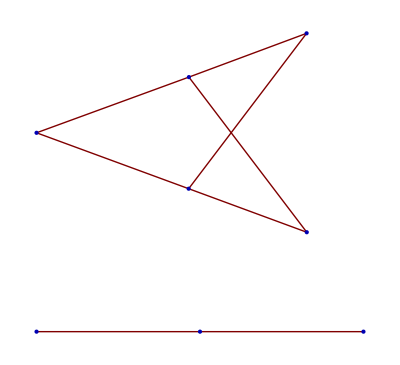

```mathematica
GraphPlot[A1]
```

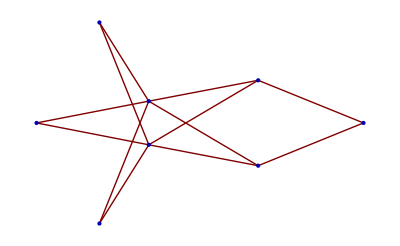

```mathematica
GraphPlot[A2]
```